```mathematica
(*Mathematica*)
```

```mathematica
Clear[f,g,h1,h2,h3]
```

```mathematica
(*Shannon entropy for two value probaility*)
```

```mathematica
h1[x_]=-x*Log[x]-(1-x)*Log[1-x]
```

-(1-x) Log[1-x]-x Log[x]

```mathematica
(* Farey ray-tional number entropy*)
```

```mathematica
h2[x_]=If[x>0&&x<=1/2,-(x/(1-x))*Log[x/(1-x)],-((1-x)/x)*Log[(1-x)/x]]
```

If[x>0&&x≤1/2,-(x Log[x/(1-x)])/(1-x),-((1-x) Log[(1-x)/x])/x]

```mathematica
Plot[{h1[x],h2[x]},{x,0,1}]
```

```mathematica
Plot[{h2[h2[x]],h1[h2[x]],h2[h1[x]],h1[h1[x]]},{x,0,1}]
```

```mathematica
(*the functions plotted against each other*)
```

```mathematica
ParametricPlot[{h1[x],h2[x]},{x,0,1}]
```

```mathematica
ParametricPlot[{h1[h2[x]],h2[h1[x]]},{x,0,1}]
```

```mathematica
ParametricPlot[{h2[h2[x]],h1[h1[x]]},{x,0,1}]
```

```mathematica
(*Octant sphere Gauss map of the two entropies*)
```

```mathematica
x1={2*h1[x],2*h2[x],1-h1[x]^2-h2[x]^2}/(1+h1[x]^2+h2[x]^2);
x2={-2*h1[x],2*h2[x],1-h1[x]^2-h2[x]^2}/(1+h1[x]^2+h2[x]^2);
x3={2*h1[x],-2*h2[x],1-h1[x]^2-h2[x]^2}/(1+h1[x]^2+h2[x]^2);
x4={2*h1[x],2*h2[x],-(1-h1[x]^2-h2[x]^2)}/(1+h1[x]^2+h2[x]^2);
x5=-{2*h1[x],2*h2[x],1-h1[x]^2-h2[x]^2}/(1+h1[x]^2+h2[x]^2);
x6=-{-2*h1[x],2*h2[x],1-h1[x]^2-h2[x]^2}/(1+h1[x]^2+h2[x]^2);
x7=-{2*h1[x],-2*h2[x],1-h1[x]^2-h2[x]^2}/(1+h1[x]^2+h2[x]^2);
x8=-{2*h1[x],2*h2[x],-(1-h1[x]^2-h2[x]^2)}/(1+h1[x]^2+h2[x]^2);
```

```mathematica
ParametricPlot3D[{2*h1[x],2*h2[x],1-h1[x]^2-h2[x]^2}/(1+h1[x]^2+h2[x]^2),{x,0,1}]
```

```mathematica
ParametricPlot3D[{x1,x2,x3,x4,x5,x6,x7,x8},{x,0,1}]
```

```mathematica
(*Farey function*)
```

```mathematica
f[x_]=If[x>0&&x<=1/2,(x/(1-x)),((1-x)/x)]
```

If[x>0&&x≤1/2,x/(1-x),(1-x)/x]

```mathematica
Plot[f[x],{x,0,1}]
```

```mathematica
(*Hyper-Farey function*)
```

```mathematica
g[x_]=f[f[x]]
```

If[If[x>0&&x≤1/2,x/(1-x),(1-x)/x]>0&&If[x>0&&x≤1/2,x/(1-x),(1-x)/x]≤1/2,If[x>0&&x≤1/2,x/(1-x),(1-x)/x]/(1-If[x>0&&x≤1/2,x/(1-x),(1-x)/x]),(1-If[x>0&&x≤1/2,x/(1-x),(1-x)/x])/If[x>0&&x≤1/2,x/(1-x),(1-x)/x]]

```mathematica
Plot[{f[x],f[f[x]],f[f[f[x]]]},{x,0,1}]
```

```mathematica
h3[x_]=-g[x]*Log[g[x]]
```

-If[If[x>0&&x≤1/2,x/(1-x),(1-x)/x]>0&&If[x>0&&x≤1/2,x/(1-x),(1-x)/x]≤1/2,If[x>0&&x≤1/2,x/(1-x),(1-x)/x]/(1-If[x>0&&x≤1/2,x/(1-x),(1-x)/x]),(1-If[x>0&&x≤1/2,x/(1-x),(1-x)/x])/If[x>0&&x≤1/2,x/(1-x),(1-x)/x]] Log[If[If[x>0&&x≤1/2,x/(1-x),(1-x)/x]>0&&If[x>0&&x≤1/2,x/(1-x),(1-x)/x]≤1/2,If[x>0&&x≤1/2,x/(1-x),(1-x)/x]/(1-If[x>0&&x≤1/2,x/(1-x),(1-x)/x]),(1-If[x>0&&x≤1/2,x/(1-x),(1-x)/x])/If[x>0&&x≤1/2,x/(1-x),(1-x)/x]]]

```mathematica
(* four hump Hyper-Farey entropy*)
```

```mathematica
Plot[{h1[x],h2[x],h3[x]},{x,0,1}]
```

```mathematica
Clear[f]
```

```mathematica
(*Bi-Farey*)
```

```mathematica
f[x_]:=(x/(1-x))/;0<=x<=1/4
f[x_]:=((1-x)/x)/6-1/6/;1/4<x≤1/2
f[x_]:=(x/(1-x))/6-1/6/;1/2<=x≤3/4
f[x_]:=((1-x)/x)/;3/4<x<=1
```

```mathematica
Plot[f[x],{x,0,1}]
```

```mathematica
(*entropy function*)
```

```mathematica
hd[x_]=-f[x]*Log[f[x]]
```

-f[x] Log[f[x]]

```mathematica
Plot[hd[x],{x,0,1}]
```

```mathematica
Plot[{h1[x],h2[x],hd[x]},{x,0,1}]
```

```mathematica
(*2nd Farey type*)
```

```mathematica
Clear[f]
```

```mathematica
(*Bi-Farey 2nd derivative*)
```

```mathematica
D[(x/(1-x)),{x,2}]
```

2/(1-x)^2+(2 x)/(1-x)^3

```mathematica
D[((1-x)/x)/6-1/6,{x,2}]
```

(1-x)/(3 x^3)+1/(3 x^2)

```mathematica
D[(x/(1-x))/6-1/6,{x,2}]
```

1/(3 (1-x)^2)+x/(3 (1-x)^3)

```mathematica
D[((1-x)/x),{x,2}]
```

(2 (1-x))/x^3+2/x^2

```mathematica
f[x_]:=(2/(1-x)^2+(2 x)/(1-x)^3-2)/2.7/;0<=x<=1/4
f[x_]:=(((1-x)/(3 x^3)+1/(3 x^2))/7-1/2+0.14)/2.7/;1/4<x≤1/2
f[x_]:=((1/(3 (1-x)^2)+x/(3 (1-x)^3))/7-1/2+0.14)/2.7/;1/2<=x≤3/4
f[x_]:=((2 (1-x))/x^3+2/x^2-2)/2.7/;3/4<x<=1
```

```mathematica
Plot[f[x],{x,0,1}]
```

```mathematica
(*entropy function*)
```

```mathematica
hd[x_]=-f[x]*Log[f[x]]
```

-f[x] Log[f[x]]

```mathematica
Plot[hd[x],{x,0,1}]
```

```mathematica
Plot[{h1[x],h2[x],hd[x]},{x,0,1}]
```

```mathematica
(*end*)
```

```mathematica
(*Mathematica*)
```

```mathematica
Clear[f,g,h,k,x]
```

```mathematica
(*Farey function*)
```

```mathematica
f[x_]=If[x>0&&x<=1/2,(x/(1-x)),((1-x)/x)]
```

If[x>0&&x≤1/2,x/(1-x),(1-x)/x]

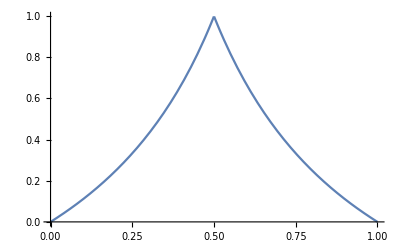

```mathematica
Plot[f[x],{x,0,1}]
```

```mathematica
(*Hyper-Farey function: Cantor-Farey:peaks at {1/3,2/3} instead of 1/2*)
```

```mathematica
g[x_]=f[f[x]]
```

If[If[x>0&&x≤1/2,x/(1-x),(1-x)/x]>0&&If[x>0&&x≤1/2,x/(1-x),(1-x)/x]≤1/2,If[x>0&&x≤1/2,x/(1-x),(1-x)/x]/(1-If[x>0&&x≤1/2,x/(1-x),(1-x)/x]),(1-If[x>0&&x≤1/2,x/(1-x),(1-x)/x])/If[x>0&&x≤1/2,x/(1-x),(1-x)/x]]

```mathematica
Plot[{f[f[x]],g[x]},{x,0,1}]
```

```mathematica
ff[x_]=g[Mod[Abs[x],1]]
```

If[If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]>0&&If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]≤1/2,If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]/(1-If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]),(1-If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]])/If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]]

```mathematica
Plot[g[Mod[Abs[x],1]],{x,0,2}]
```

```mathematica
s0=Log[2]/Log[3]
```

Log[2]/Log[3]

```mathematica
hh[x_]=Sum[ff[2^k*x]/2^(s0*k),{k,0,20}];
```

```mathematica
kk[x_]=Sum[ff[2^k*(x+1/3)]/2^(s0*k),{k,0,20}];
ll[x_]=Sum[ff[2^k*(x-1/3)]/2^(s0*k),{k,0,20}];
```

```mathematica
g0=ParametricPlot[{hh[t],kk[t]},{t,0,1},PlotPoints->200,Axes->False,ColorFunction->Hue,ImageSize->2000];
```

```mathematica
g1=ParametricPlot3D[{hh[t],kk[t],ll[t]},{t,0,1},PlotPoints->200,Axes->False,ColorFunction->Hue,ImageSize->2000,ViewPoint->{2,2,2}];
```

```mathematica
Export["biscuit_Hyper_Farey_3rdPhase_scale3_color.jpg",GraphicsGrid[{{g0,g1}},ImageSize->{4000,2000}]]
```

biscuit_Hyper_Farey_3rdPhase_scale3_color.jpg

```mathematica
(*end*)
```